## EWS plot for Fussmann MODEL

## Import data

### EWS data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/hopf_fussmann_2000"];
```

```mathematica
(* data has form {deltaVals,varVals,cvVals,acVals,SmaxVals,aicFoldVals,aicHopfVals} *)
ewsRaw=Import["model/data_export/ews_stat/ews_delta.csv"];
```

### Bifurcation data

```mathematica
bifPtsChlor=Import["data/bifPtsChlor.mat"];
bifPtsBrach=Import["data/bifPtsBrach.mat"];
```

### General figure parameters

```mathematica
imgs=400;
aratio=0.25;
padding={{60,60},{20,20}};
{{padLeft,padRight},{padBottom,padTop}}=padding;
lt=0.006;
colChlor=Darker[TMBcolours[[1]],0.15];
colBrach=Darker[TMBcolours[[4]],0.15];
{colChlor,colBrach}
labelPos=Scaled[{0.04,0.85}];
```

{RGBColor[0.31315445, 0.43076214999999995, 0.6033283],RGBColor[0.7841471, 0.3277821, 0.17780215]}

```mathematica
deltaVals=Union[ewsRaw[[2;;,2]]];
```

## Bifurcation diagram

```mathematica
deltaVals=Union[ewsRaw[[2;;,2]]];
```

```mathematica
nodeSections2=Table[DeleteCases[nodeSections[[i]],{x_,_,_,_}/;x>1.5],{i,1,Length[nodeSections]}]
```

```mathematica
bifPtsChlor2=Table[DeleteCases[bifPtsChlor[[i]],{x_,_}/;x>1.6],{i,1,Length[bifPtsChlor]}];
```

```mathematica
bifPtsChlor2
```

{{{1.50318,-1.5736×10^-20},{1.50556,-1.57665×10^-24},{1.50873,-5.63145×10^-26},{1.51188,3.64394×10^-25},{1.51502,8.21615×10^-25},{1.51815,1.79147×10^-25},{1.52127,-1.81946×10^-25},68,{1.43823,-1.01433×10^-24},{1.43482,2.34727×10^-25},{1.4314,3.84962×10^-25},{1.42797,-1.11298×10^-24},{1.42705,-9.5975×10^-30},{1.4236,1.58853×10^-25}},5,{1}}
 |  |  |  |

```mathematica
bifPtsChlor//Dimensions
```

{7}

```mathematica
(* bifurcation values *)
```

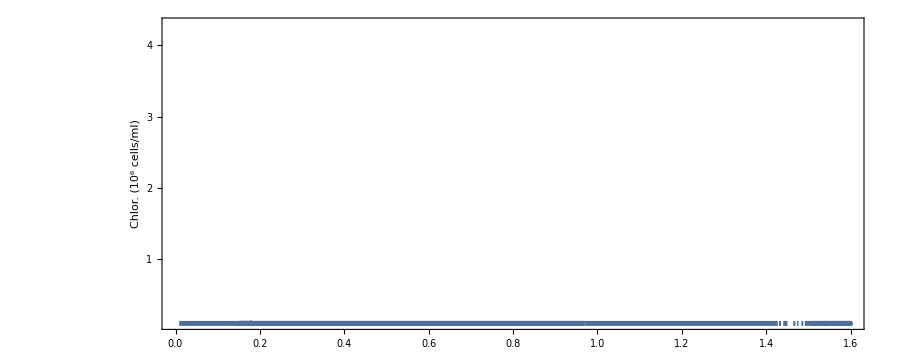

```mathematica
(* Chlorella bifurcation plot *)
bifPlotChlor=ListLinePlot[bifPtsChlor2,
PlotStyle->Table[{colChlor,Thickness[lt]},{i,1,Length[bifPtsChlor]}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.6},{0,4.2}*1000000},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Chlor. (10^6 cells/ml)",Style["Brach. (females/ml)",White]},{"",""}},
FrameTicks->{{Transpose[{Range[-4/40,4]*1000000,Range[0,4]}],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False,
ImagePadding->padding]
```

```mathematica
(* brachionus bif *)
bifPlotBrach=ListLinePlot[bifPtsBrach,
PlotRange->{{0,1.5},{-59/40,59}},
PlotStyle->Table[{colBrach,Thickness[lt]},{i,1,Length[bifPtsBrach]}],
LabelStyle->14,
InterpolationOrder->1,
Frame->{{False,True},{True,True}},
FrameLabel->{{Style["Chlor. (10^6 cells/ml)",White],"Brach. (females/ml)"},{"",""}},
FrameTicks->{{None,Range[0,60,10]},{None,None}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False,
ImagePadding->padding];
```

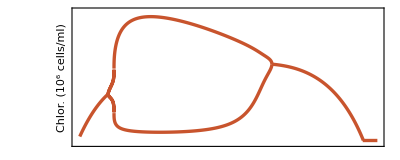
-Graphics--Graphics-

```mathematica
(* put together *)
bifPlot=Overlay[{bifPlotChlor,bifPlotBrach}]
```

## Plots of EWS against delta

### Variance

```mathematica
index=Position[ewsChlorRaw[[1]],"Variance"][[1,1]];
```

```mathematica
varChlor=ewsChlorRaw[[2;;,index]];
varBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
varPlotChlor=ListLinePlot[Transpose[{deltaVals,varChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Var",""},{"",""}},
FrameTicks->{{Range[0,1,0.2],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["b",14,Bold],labelPos]}
];
```

```mathematica
varPlotBrach=ListLinePlot[Transpose[{deltaVals,varBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Var"},{"",""}},
FrameTicks->{{None,Range[0,50,10]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

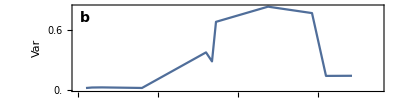
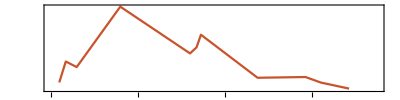

```mathematica
varPlot=Overlay[{varPlotChlor,varPlotBrach}]
```

### Coefficient of variation

```mathematica
ewsChlorRaw[[1]]
```

{Delta,Variance,Coefficient of variation,Lag-1 AC,Lag-2 AC,Lag-10 AC,Smax,AIC fold,AIC hopf,AIC null}

```mathematica
index=Position[ewsChlorRaw[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
cvarChlor=ewsChlorRaw[[2;;,index]];
cvarBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
cvarPlotChlor=ListLinePlot[Transpose[{deltaVals,cvarChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"C.V.",""},{"",""}},
FrameTicks->{{Range[0,1,0.2],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}];
```

```mathematica
cvarPlotBrach=ListLinePlot[Transpose[{deltaVals,cvarBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","C.V."},{"",""}},
FrameTicks->{{None,Range[0,10,0.2]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

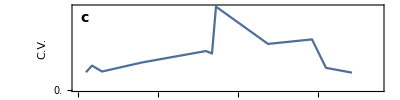
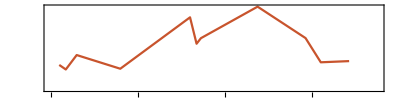

```mathematica
cvarPlot=Overlay[{cvarPlotChlor,cvarPlotBrach}]
```

### Lag-1 AC

```mathematica
index=Position[ewsChlorRaw[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
acChlor=ewsChlorRaw[[2;;,index]];
acBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
acPlotChlor=ListLinePlot[Transpose[{deltaVals,acChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-1 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}];
```

```mathematica
acPlotBrach=ListLinePlot[Transpose[{deltaVals,acBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-1 AC"},{"",""}},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

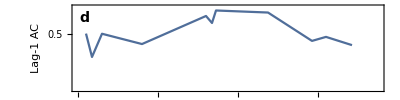
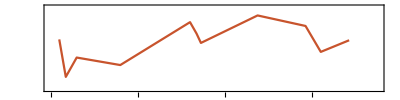

```mathematica
acPlot=Overlay[{acPlotChlor,acPlotBrach}]
```

### Lag-2 AC

```mathematica
index=Position[ewsChlorRaw[[1]],"Lag-2 AC"][[1,1]];
```

```mathematica
acChlor=ewsChlorRaw[[2;;,index]];
acBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
acPlotChlor=ListLinePlot[Transpose[{deltaVals,acChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-2 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}];
```

```mathematica
acPlotBrach=ListLinePlot[Transpose[{deltaVals,acBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-2 AC"},{"",""}},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

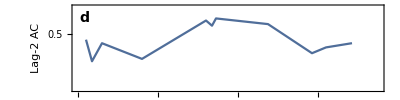
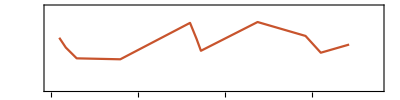

```mathematica
ac2Plot=Overlay[{acPlotChlor,acPlotBrach}]
```

### Lag-10 AC

```mathematica
index=Position[ewsChlorRaw[[1]],"Lag-10 AC"][[1,1]];
```

```mathematica
acChlor=ewsChlorRaw[[2;;,index]];
acBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
acPlotChlor=ListLinePlot[Transpose[{deltaVals,acChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-1,1}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-10 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}];
```

```mathematica
acPlotBrach=ListLinePlot[Transpose[{deltaVals,acBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-1,1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-10 AC"},{"",""}},
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

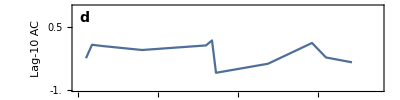
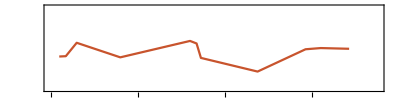

```mathematica
ac2Plot=Overlay[{acPlotChlor,acPlotBrach}]
```

### Smax

```mathematica
index=Position[ewsChlorRaw[[1]],"Smax"][[1,1]];
```

```mathematica
smaxChlor=ewsChlorRaw[[2;;,index]];
smaxBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
smaxPlotChlor=ListLinePlot[Transpose[{deltaVals,smaxChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"S_max",""},{"",""}},
FrameTicks->{{Range[0,10,0.1],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["e",14,Bold],labelPos]}];
```

```mathematica
smaxPlotBrach=ListLinePlot[Transpose[{deltaVals,smaxBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},All},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","S_max"},{"",""}},
FrameTicks->{{None,Range[0,10,1]//N},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

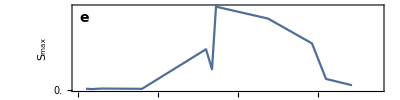
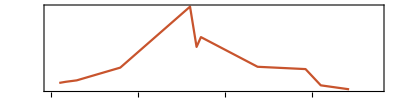

```mathematica
smaxPlot=Overlay[{smaxPlotChlor,smaxPlotBrach}]
```

### AIC weight fold

```mathematica
index=Position[ewsChlorRaw[[1]],"AIC fold"][[1,1]];
```

```mathematica
aicfoldChlor=ewsChlorRaw[[2;;,index]];
aicfoldBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
aicfoldPlotChlor=ListLinePlot[Transpose[{deltaVals,aicfoldChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_fold(C)",""},{"",""}},
FrameTicks->{{Range[0,1,0.2],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

```mathematica
aicfoldPlotBrach=ListLinePlot[Transpose[{deltaVals,aicfoldBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_fold(B)"},{"",""}},
FrameTicks->{{None,Range[0,1,0.2]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

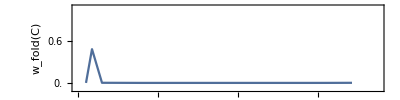
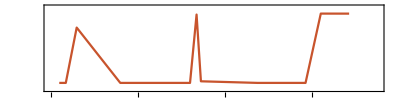

```mathematica
aicfoldPlot=Overlay[{aicfoldPlotChlor,aicfoldPlotBrach}]
```

### AIC weight hopf

```mathematica
index=Position[ewsChlorRaw[[1]],"AIC hopf"][[1,1]];
```

```mathematica
aichopfChlor=ewsChlorRaw[[2;;,index]];
aichopfBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
aichopfPlotChlor=ListLinePlot[Transpose[{deltaVals,aichopfChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.1,1.3}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_hopf",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*1.3,padTop}},
Epilog->{Directive[{Black}],Text[Style["f",14,Bold],labelPos]}];
```

```mathematica
aichopfPlotBrach=ListLinePlot[Transpose[{deltaVals,aichopfBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.1,1.3}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_hopf"},{"Dilution rate δ (per day)",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*2.2,padTop}}];
```

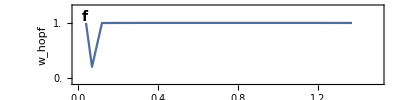
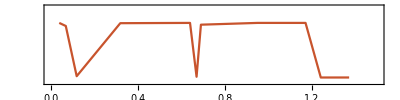

```mathematica
aichopfPlot=Overlay[{aichopfPlotChlor,aichopfPlotBrach}]
```

### AIC weight Null

```mathematica
index=Position[ewsChlorRaw[[1]],"AIC null"][[1,1]];
```

```mathematica
aicNullChlor=ewsChlorRaw[[2;;,index]];
aicNullBrach=ewsBrachRaw[[2;;,index]];
```

```mathematica
aicNullPlotChlor=ListLinePlot[Transpose[{deltaVals,aicNullChlor}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.1,1.2}},
PlotStyle->colChlor,
Frame->{{True,False},{True,True}},
FrameLabel->{{"w_null(C)",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*1.3,padTop}},
Epilog->{Directive[{Black}],Text[Style["f",14,Bold],labelPos]}];
```

```mathematica
aicNullPlotBrach=ListLinePlot[Transpose[{deltaVals,aicNullBrach}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.1,1.2}},
PlotStyle->colBrach,
Frame->{{False,True},{True,True}},
FrameLabel->{{"","w_null(B)"},{"Dilution rate δ (per day)",""}},
FrameTicks->{{None,Range[0,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*2.2,padTop}}];
```

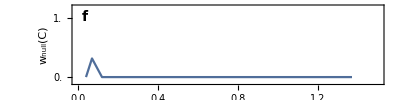
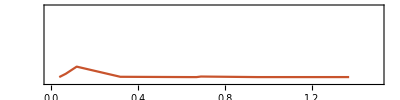

```mathematica
aicNullPlot=Overlay[{aicNullPlotChlor,aicNullPlotBrach}]
```

## Grid all plots together

```mathematica
ewsFussmannPlot=Grid[{{bifPlot},{varPlot},{cvarPlot},{acPlot},{smaxPlot},{aichopfPlot}},Spacings->{0,-1.5}]
```

-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics-

```mathematica
Export["figures/ews_series.png",ewsFussmannPlot,ImageResolution->200];
```